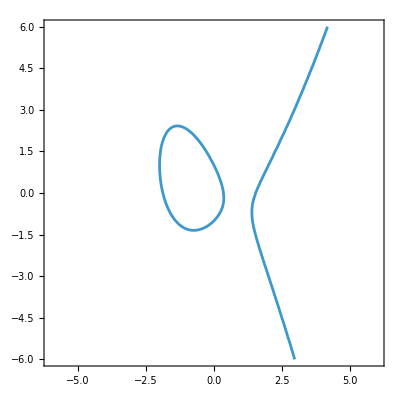

```mathematica
ContourPlot[y^2+x y ==x^3-3x+1, {x, -6, 6}, {y, -6, 6}]
```

```mathematica
x^2 y + x y^2 - x y z/u +m y z^2 + z^3/.{y->y-1/m z}//Expand
%/.{y->a y+r x+s z, x->y+x}//Simplify//Expand
Coefficient[%, {x y^2, x^2 y}]
```

x^2 y+x y^2-(x^2 z)/m-(2 x y z)/m-(x y z)/u+(x z^2)/m^2+(x z^2)/(m u)+m y z^2

r x^3+r^2 x^3+a x^2 y+2 r x^2 y+2 a r x^2 y+r^2 x^2 y+2 a x y^2+a^2 x y^2+r x y^2+2 a r x y^2+a y^3+a^2 y^3-(x^2 z)/m-(2 r x^2 z)/m+s x^2 z+2 r s x^2 z-(r x^2 z)/u-(2 x y z)/m-(2 a x y z)/m-(2 r x y z)/m+2 s x y z+2 a s x y z+2 r s x y z-(a x y z)/u-(r x y z)/u-(y^2 z)/m-(2 a y^2 z)/m+s y^2 z+2 a s y^2 z-(a y^2 z)/u+(x z^2)/m^2+m r x z^2-(2 s x z^2)/m+s^2 x z^2+(x z^2)/(m u)-(s x z^2)/u+(y z^2)/m^2+a m y z^2-(2 s y z^2)/m+s^2 y z^2+(y z^2)/(m u)-(s y z^2)/u+m s z^3

{2 a+a^2+r+2 a r,a+2 r+2 a r+r^2}

```mathematica
x^2 y + x y^2 - x y z/u +m y z^2 + z^3/.{z->1}/.{y->y-1/m}//Simplify//Expand
%/.{x->y,y->x}
Z^3*%/.{x->X/Z, y->Y/Z}//Expand
{F3, F2, F1} = CoefficientList[%, Z]
```

x/m^2+x/(m u)-x^2/m+m y-(2 x y)/m-(x y)/u+x^2 y+x y^2

m x+y/m^2+y/(m u)-(2 x y)/m-(x y)/u+x^2 y-y^2/m+x y^2

X^2 Y+X Y^2-(2 X Y Z)/m-(X Y Z)/u-(Y^2 Z)/m+m X Z^2+(Y Z^2)/m^2+(Y Z^2)/(m u)

{X^2 Y+X Y^2,-(2 X Y)/m-(X Y)/u-Y^2/m,m X+Y/m^2+Y/(m u)}

```mathematica
{s8, s9} = Coefficient[F1, {X, Y}]
```

{m,1/m^2+1/(m u)}

```mathematica
e2 = F2/.{X->s9, Y->-s8}//Expand
```

2/m^2-m+1/u^2+3/(m u)

```mathematica
e3 = F3/.{X->s9, Y->-s8}//Expand
```

1-1/m^3-1/(m u^2)-2/(m^2 u)+m/u

e2, e3 should not simultaneously be 0

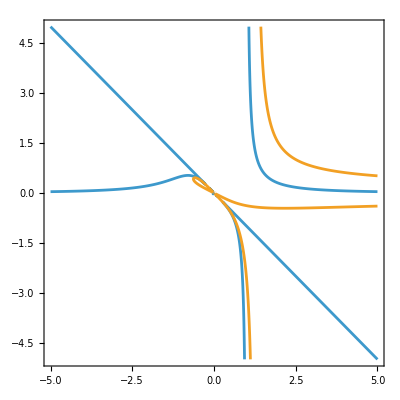

```mathematica
ContourPlot[{1-1/m^3-1/(m u^2)-2/(m^2 u)+m/u==0, 2/m^2-m+1/u^2+3/(m u)==0}, {m, -5, 5}, {u, -5, 5}, PlotPoints->100, MaxRecursion->4]
```

at this point we assume generic e3 and proceed TODO: see what happens when e3 = 0

```mathematica
(* check that Q lies on the curve *)
F3 + F2 Z + F1 Z^2/.{X->-e2 s9, Y->e2 s8, Z->e3}//Expand
```

0

```mathematica
(* change of coordinates and check that Q becomes [0, 0, 1] *)
c1 = F3 + F2 Z + F1 Z^2/.{X->X-e2 s9/e3 Z, Y->Y+e2 s8/e3 Z}//Expand;
%/.{X->0, Y->0, Z->1}//Simplify
```

0

```mathematica
c1//Simplify;
{f3, f2, f1} = CoefficientList[%, Z];
```

```mathematica
phi3 = f3/.{X->1, Y->t}//Simplify
```

t (1+t)

```mathematica
phi2 = f2/.{X->1, Y->t}//Simplify
```

-1/(m u (m+u) (m+u-m^3 u))(m^5 (1+t) u-m^2 t (4+3 t) u-m t (5+3 t) u^2+m^4 (3+5 t) u^2-t (2+t) u^3-m^6 (1+2 t) u^3-m^3 (t+t^2-2 u^3-4 t u^3))

```mathematica
phi1 = f1/.{X->1, Y->t}//Simplify
```

(10 m^2 t u^3-3 m^10 u^4+5 m t u^4+m^12 u^5+t u^5+m^9 u^2 (1+2 t-3 u^3)+m^8 (1+t) (-1+6 u^3)+m^5 (t-19 u^3-28 t u^3)+m^4 (5 t u-12 u^4-17 t u^4)+m^3 (10 t u^2-3 u^5-4 t u^5)+m^6 u^2 (-15+4 u^3+2 t (-11+u^3))+m^7 u (-6+9 u^3+t (-8+6 u^3)))/(m^2 u (m+u)^2 (m+u-m^3 u)^2)

```mathematica
delt = phi2^2-4phi1 phi3//Simplify
```

((-m^5 (1+t) u+m^2 t (4+3 t) u+m t (5+3 t) u^2-m^4 (3+5 t) u^2+t (2+t) u^3+m^6 (1+2 t) u^3+m^3 (t+t^2-2 u^3-4 t u^3))^2-4 t (1+t) u (10 m^2 t u^3-3 m^10 u^4+5 m t u^4+m^12 u^5+t u^5+m^9 u^2 (1+2 t-3 u^3)+m^8 (1+t) (-1+6 u^3)+m^5 (t-19 u^3-28 t u^3)+m^4 (5 t u-12 u^4-17 t u^4)+m^3 (10 t u^2-3 u^5-4 t u^5)+m^6 u^2 (-15+4 u^3+2 t (-11+u^3))+m^7 u (-6+9 u^3+t (-8+6 u^3))))/(m^2 u^2 (m+u)^2 (m+u-m^3 u)^2)

```mathematica
(* check that phi and delt are defined correctly *)
c2 = c1 /. Z -> 1 /. {X -> x, Y -> y};
% /. {y -> t x} /. {x -> (-phi2 + Sqrt[delt])/2/phi3} // Simplify
```

0

```mathematica
rho = tp^4 * delt/.{t->-s8/s9 + 1/tp}//Simplify
```

(m^2 (10+8 tp+tp^2) u^3-m^8 tp (4+15 tp+12 tp^2) u^3+m (5+2 tp) u^4+4 m^10 tp^2 (2+3 tp) u^4+u^5-4 m^12 tp^3 u^5-2 m^7 tp (1+tp) u (1+4 (1+3 tp) u^3)+m^9 tp^2 u^2 (1+4 (2+3 tp) u^3)-2 m^6 tp u^2 (1+2 u^3+tp^2 (-2+6 u^3)+tp (-2+8 u^3))+m^4 u (5+12 tp^3 u^3+2 tp (4+5 u^3)+3 tp^2 (1+8 u^3))+m^3 u^2 (10+4 tp^3 u^3+4 tp (3+u^3)+tp^2 (3+8 u^3))+m^5 (1+12 tp^3 u^3+tp (2+6 u^3)+tp^2 (1+22 u^3)))/(m^2 u^2 (m+u) (m+u-m^3 u)^2)

```mathematica
c = Coefficient[rho, tp, 3]//Simplify
```

(4 m (m+u-m^3 u))/(m+u)

```mathematica
CoefficientList[rho, tp]//Simplify
```

{(m+u)^4/(m^2 u^2 (m+u-m^3 u)^2),(2 (m+u) (m+u+2 m^2 u^2))/(m u^2 (m+u-m^3 u)),8 m+1/u^2,(4 m (m+u-m^3 u))/(m+u)}

```mathematica
ysq = 4c^2 rho/.{tp->x/c}//Simplify
CoefficientList[%, x]//Simplify
```

(4 (8 u x+x^2+16 m^2 (1+u^2 x)+8 m (4 u+x+u^2 x^2)+u^2 (16+x^3)))/u^2

{(64 (m+u)^2)/u^2,(32 (m+u+2 m^2 u^2))/u^2,4 (8 m+1/u^2),4}

```mathematica
a = Coefficient[ysq, x, 2]
```

(4 (1+8 m u^2))/u^2

```mathematica
ysq/.{x->X-a/12, y->Y}//Expand
CoefficientList[%, X]//Simplify
```

64-(512 m^3)/27+8/(27 u^6)-(32 m)/(9 u^4)-32/(3 u^3)+(128 m^2)/(9 u^2)+(128 m)/(3 u)-(64 m^2 X)/3-(4 X)/(3 u^4)+(32 m X)/(3 u^2)+(32 X)/u+4 X^3

{-(8 (-1+12 m u^2+36 u^3-48 m^2 u^4-144 m u^5-216 u^6+64 m^3 u^6))/(27 u^6),-(4 (1-8 m u^2-24 u^3+16 m^2 u^4))/(3 u^4),0,4}

## Recheck

```mathematica
x+y+1/x/y+m/x-1/u
x y * %//Expand
%/.{y->y-1/m}//Expand
%/.{x->y,y->x}
F = Z^3 * %/.{x->X/Z, y->Y/Z}//Expand
{F3, F2, F1} = Simplify@CoefficientList[%, Z]
```

-1/u+m/x+x+1/(x y)+y

1+m y-(x y)/u+x^2 y+x y^2

x/m^2+x/(m u)-x^2/m+m y-(2 x y)/m-(x y)/u+x^2 y+x y^2

m x+y/m^2+y/(m u)-(2 x y)/m-(x y)/u+x^2 y-y^2/m+x y^2

X^2 Y+X Y^2-(2 X Y Z)/m-(X Y Z)/u-(Y^2 Z)/m+m X Z^2+(Y Z^2)/m^2+(Y Z^2)/(m u)

{X Y (X+Y),-(Y (m X+u (2 X+Y)))/(m u),(m^3 X+Y+(m Y)/u)/m^2}

```mathematica
F1
{A, B} = Simplify@Coefficient[%, {X, Y}]
```

(m^3 X+Y+(m Y)/u)/m^2

{m,(m+u)/(m^2 u)}

```mathematica
e2 = F2/.{X->B, Y->-A}//Simplify
```

2/m^2-m+1/u^2+3/(m u)

```mathematica
e3 = F3/.{X->B, Y->-A}//Simplify
```

((m+u) (-m-u+m^3 u))/(m^3 u^2)

```mathematica
Qcoords = Simplify@{-e2 B, e2 A, e3}
```

{((m+u) (-m^2-3 m u-2 u^2+m^3 u^2))/(m^4 u^3),2/m-m^2+m/u^2+3/u,((m+u) (-m-u+m^3 u))/(m^3 u^2)}

```mathematica
F1/.Thread[{X,Y,Z}->Qcoords]//Simplify
```

0

```mathematica
F/.Thread[{X,Y,Z}->Qcoords]//Simplify
```

0

```mathematica
Solve[2/m^2-m+1/u^2+3/(m u)==0, u]
```

{{u→(-3 m+√(m^2+4 m^5))/(2 (2-m^3))},{u→(3 m+√(m^2+4 m^5))/(2 (-2+m^3))}}

```mathematica
Solve[{((m+u) (u-(m+u)/m^3))/u^2==0}, {u}]
e2/.%//Simplify
```

{{u→-m},{u→m/(-1+m^3)}}

{-m,m^4}

```mathematica
<<MaTeX`;
texStyle={FontSize->12, FontFamily->"Times New Roman"}; 
SetOptions[MaTeX,FontSize->12,"Preamble"->{"\\usepackage[english]{babel}","\\usepackage{amsmath,amssymb}", "\\usepackage{lmodern}"}];
imgWidth=218;
SetOptions[$FrontEnd,PrintingStyleEnvironment->"Working"]
```

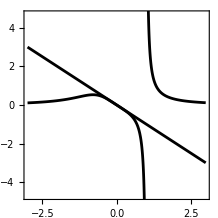

/Users/rishi/Developer/localf1/figures/e3Vanish.pdf

```mathematica
plt1 = ParametricPlot[{{m, -m}, {m, m/(-1+m^3)}}, {m, -3, 3},
BaseStyle->texStyle,
AspectRatio->1,
PlotStyle->Black,
Frame->True,
FrameLabel->MaTeX/@{"m", "u"},
ImageSize->imgWidth
]
(*Export["/Users/rishi/Developer/localf1/figures/e3Vanish.pdf", plt1]*)
```

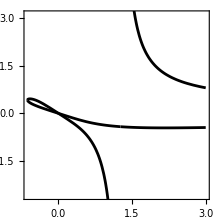

/Users/rishi/Developer/localf1/figures/e2Vanish.pdf

```mathematica
plt2 = ParametricPlot[{{m, (-3 m+√(m^2+4 m^5))/(2 (2-m^3))}, {m, (3 m+√(m^2+4 m^5))/(2 (-2+m^3))}}, {m, -3, 3},
BaseStyle->texStyle,
AspectRatio->1,
PlotStyle->Directive[Black],
Frame->True,
FrameLabel->MaTeX/@{"m", "u"},
ImageSize->imgWidth
]
(*Export["/Users/rishi/Developer/localf1/figures/e2Vanish.pdf", plt2]*)
```

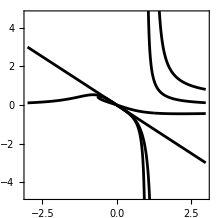

```mathematica
Show[plt1, plt2]
```

```mathematica
FullSimplify[F/.{X->Xp-B e2/e3 Zp, Y->Yp+A e2/e3 Zp, Z->Zp}]
{f3p, f2p, f1p} = FullSimplify/@CoefficientList[%, Zp]
```

(m^6 u Xp^2 Yp+4 m^5 u^2 Xp^2 Yp-2 m^8 u^2 Xp^2 Yp+6 m^4 u^3 Xp^2 Yp-6 m^7 u^3 Xp^2 Yp+m^10 u^3 Xp^2 Yp+4 m^3 u^4 Xp^2 Yp-6 m^6 u^4 Xp^2 Yp+2 m^9 u^4 Xp^2 Yp+m^2 u^5 Xp^2 Yp-2 m^5 u^5 Xp^2 Yp+m^8 u^5 Xp^2 Yp+m^6 u Xp Yp^2+4 m^5 u^2 Xp Yp^2-2 m^8 u^2 Xp Yp^2+6 m^4 u^3 Xp Yp^2-6 m^7 u^3 Xp Yp^2+m^10 u^3 Xp Yp^2+4 m^3 u^4 Xp Yp^2-6 m^6 u^4 Xp Yp^2+2 m^9 u^4 Xp Yp^2+m^2 u^5 Xp Yp^2-2 m^5 u^5 Xp Yp^2+m^8 u^5 Xp Yp^2-m (m+u) (-m+(-1+m^3) u) (m^3 u (-m^2-3 m u+(-2+m^3) u^2) Xp^2+(-m+(-1+m^3) u) (-m^2-3 m u+2 (-1+m^3) u^2) Xp Yp+(m+u)^3 Yp^2) Zp+(m^3 (-m^5-6 m^4 u+m^3 (-15+m^3) u^2+m^2 (-19+6 m^3) u^3-3 m (4-3 m^3+m^6) u^4+(-3+4 m^3-3 m^6+m^9) u^5) Xp+(m+u)^3 (m^2-m^5+2 m u-5 m^4 u+u^2-4 m^3 u^2+2 m^6 u^2) Yp) Zp^2)/(m^2 u (m+u)^2 (m+u-m^3 u)^2)

{Xp Yp (Xp+Yp),(m^3 u (m^2+3 m u-(-2+m^3) u^2) Xp^2-(-m+(-1+m^3) u) (-m^2-3 m u+2 (-1+m^3) u^2) Xp Yp-(m+u)^3 Yp^2)/(m u (m+u) (-m+(-1+m^3) u)),(m^3 (-m^5-6 m^4 u+m^3 (-15+m^3) u^2+m^2 (-19+6 m^3) u^3-3 m (4-3 m^3+m^6) u^4+(-3+4 m^3-3 m^6+m^9) u^5) Xp+(m+u)^3 (m^2-m^5+2 m u-5 m^4 u+u^2-4 m^3 u^2+2 m^6 u^2) Yp)/(m^2 u (m+u)^2 (m+u-m^3 u)^2)}

```mathematica
Map[FullSimplify[Expand[#]]&, CoefficientList[(m^3 u (m^2+3 m u-(-2+m^3) u^2) Xp^2-(-m+(-1+m^3) u) (-m^2-3 m u+2 (-1+m^3) u^2) Xp Yp-(m+u)^3 Yp^2)/(m u (m+u) (-m+(-1+m^3) u)), {Xp, Yp}], Infinity]
```

{{0,0,(m+u)^2/(m u (m+u-m^3 u))},{0,1/u+(2 (m+u-m^3 u))/(m (m+u)),0},{(m^2 (m^2+3 m u-(-2+m^3) u^2))/((m+u) (-m+(-1+m^3) u)),0,0}}

```mathematica
Map[FullSimplify[Expand[#]]&, CoefficientList[(m^3 (-m^5-6 m^4 u+m^3 (-15+m^3) u^2+m^2 (-19+6 m^3) u^3-3 m (4-3 m^3+m^6) u^4+(-3+4 m^3-3 m^6+m^9) u^5) Xp+(m+u)^3 (m^2-m^5+2 m u-5 m^4 u+u^2-4 m^3 u^2+2 m^6 u^2) Yp)/(m^2 u (m+u)^2 (m+u-m^3 u)^2), {Xp, Yp}], Infinity]
```

{{0,((m+u) (m^2-m^5+2 m u-5 m^4 u+u^2-4 m^3 u^2+2 m^6 u^2))/(m^2 u (m+u-m^3 u)^2)},{(m (-m^5-6 m^4 u+m^3 (-15+m^3) u^2+m^2 (-19+6 m^3) u^3-3 m (4-3 m^3+m^6) u^4+(-3+4 m^3-3 m^6+m^9) u^5))/(u (m+u)^2 (m+u-m^3 u)^2),0}}

```mathematica
(m (-m^5-6 m^4 u+m^3 (-15+m^3) u^2+m^2 (-19+6 m^3) u^3-3 m (4-3 m^3+m^6) u^4+(-3+4 m^3-3 m^6+m^9) u^5))/(u (m+u)^2 (m+u-m^3 u)^2)*1/(1/(u (m+u)^2 (-m-u+m^3 u)^2)m)//FullSimplify
```

-m^5-6 m^4 u+m^3 (-15+m^3) u^2+m^2 (-19+6 m^3) u^3-3 m (4-3 m^3+m^6) u^4+(-3+4 m^3-3 m^6+m^9) u^5

```mathematica
1/(u (m+u)^2 (-m-u+m^3 u)^2)m//FullSimplify
```

m/(u (m+u)^2 (m+u-m^3 u)^2)

```mathematica
CoefficientList[a Xp+b Yp, {Xp, Yp}]
```

{{0,b},{a,0}}

```mathematica
B e2/e3//Simplify
```

-(m (2/m^2-m+1/u^2+3/(m u)) u)/(m+u-m^3 u)

```mathematica
A e2/e3//Simplify
```

-(m^2 (m^2+3 m u+2 u^2-m^3 u^2))/((m+u) (m+u-m^3 u))

```mathematica
x^2 f3p + x f2p + f1p/.{Xp->1, Yp->t}//Simplify
```

(t (m+u)^3 (m^2-m^5+2 m u-5 m^4 u+u^2-4 m^3 u^2+2 m^6 u^2)+m^3 (-m^5-6 m^4 u+m^3 (-15+m^3) u^2+m^2 (-19+6 m^3) u^3-3 m (4-3 m^3+m^6) u^4+(-3+4 m^3-3 m^6+m^9) u^5))/(m^2 u (m+u)^2 (m+u-m^3 u)^2)+((-t^2 (m+u)^3+m^3 u (m^2+3 m u-(-2+m^3) u^2)-t (-m+(-1+m^3) u) (-m^2-3 m u+2 (-1+m^3) u^2)) x)/(m u (m+u) (-m+(-1+m^3) u))+t (1+t) x^2

```mathematica
delt = f2p^2-4 f1p f3p/.{Xp->1, Yp->t}//Simplify
```

((t^2 (m+u)^3-m^3 u (m^2+3 m u-(-2+m^3) u^2)+t (-m+(-1+m^3) u) (-m^2-3 m u+2 (-1+m^3) u^2))^2-4 t (1+t) u (t (m+u)^3 (m^2-m^5+2 m u-5 m^4 u+u^2-4 m^3 u^2+2 m^6 u^2)+m^3 (-m^5-6 m^4 u+m^3 (-15+m^3) u^2+m^2 (-19+6 m^3) u^3-3 m (4-3 m^3+m^6) u^4+(-3+4 m^3-3 m^6+m^9) u^5)))/(m^2 u^2 (m+u)^2 (m+u-m^3 u)^2)

```mathematica
delt/.{t->-A/B}//Simplify
```

0

```mathematica
FullSimplify[delt]
FullSimplify/@CoefficientList[ExpandAll@%, t]
```

((t^2 (m+u)^3-m^3 u (m^2+3 m u-(-2+m^3) u^2)+t (-m+(-1+m^3) u) (-m^2-3 m u+2 (-1+m^3) u^2))^2-4 t (1+t) u (t (m+u)^3 (m^2-m^5+2 m u-5 m^4 u+u^2-4 m^3 u^2+2 m^6 u^2)+m^3 (-m^5-6 m^4 u+m^3 (-15+m^3) u^2+m^2 (-19+6 m^3) u^3-3 m (4-3 m^3+m^6) u^4+(-3+4 m^3-3 m^6+m^9) u^5)))/(m^2 u^2 (m+u)^2 (m+u-m^3 u)^2)

{(m^4 (m^2+3 m u-(-2+m^3) u^2)^2)/((m+u)^2 (m+u-m^3 u)^2),(2 m (m^4+m^3 (4+m^3) u+m^2 (7+6 m^3) u^2+m (6+7 m^3-3 m^6) u^3+2 (1+m^3-m^6) u^4))/(u (m+u) (m+u-m^3 u)^2),(m^2+2 m (1+2 m^3) u+(1+18 m^3+m^6) u^2+2 m^2 (11+m^3) u^3+2 m (4+m^3-2 m^6) u^4)/(u^2 (m+u-m^3 u)^2),-(2 (m+u) (-m^2-m (2+m^3) u-(1+5 m^3) u^2+2 m^2 (-2+m^3) u^3))/(m u^2 (m+u-m^3 u)^2),(m+u)^4/(m^2 u^2 (m+u-m^3 u)^2)}

```mathematica
FullSimplify[-A/B]
```

-(m^3 u)/(m+u)

```mathematica
delt = FullSimplify[delt]
```

((t^2 (m+u)^3-m^3 u (m^2+3 m u-(-2+m^3) u^2)+t (-m+(-1+m^3) u) (-m^2-3 m u+2 (-1+m^3) u^2))^2-4 t (1+t) u (t (m+u)^3 (m^2-m^5+2 m u-5 m^4 u+u^2-4 m^3 u^2+2 m^6 u^2)+m^3 (-m^5-6 m^4 u+m^3 (-15+m^3) u^2+m^2 (-19+6 m^3) u^3-3 m (4-3 m^3+m^6) u^4+(-3+4 m^3-3 m^6+m^9) u^5)))/(m^2 u^2 (m+u)^2 (m+u-m^3 u)^2)

```mathematica
FullSimplify[delt/.{t->1/tau -(m^3 u)/(m+u)}]
rhov = FullSimplify[tau^4 %]
FullSimplify/@CoefficientList[ExpandAll@%, tau]
c = Last[%]
```

(m^5 (1+tau)^2-m^4 (1+tau) (-5+(-3+2 m^3) tau) u+m^3 (10+3 tau (4+tau)+m^3 tau (-2+tau (4+m^3+4 tau))) u^2+m^2 (10+tau (8+tau+2 m^3 (3+2 tau) (1+3 tau)-m^6 (4+3 tau (5+4 tau)))) u^3+m (5+2 tau (1-4 m^6 (1+tau) (1+3 tau)+2 m^9 tau (2+3 tau)+m^3 (5+6 tau (2+tau)))) u^4+(1-4 m^3 (-1+m^3) tau (1+tau-m^3 tau)^2) u^5)/(m^2 tau^4 u^2 (m+u) (m+u-m^3 u)^2)

(m^5 (1+tau)^2-m^4 (1+tau) (-5+(-3+2 m^3) tau) u+m^3 (10+3 tau (4+tau)+m^3 tau (-2+tau (4+m^3+4 tau))) u^2+m^2 (10+tau (8+tau+2 m^3 (3+2 tau) (1+3 tau)-m^6 (4+3 tau (5+4 tau)))) u^3+m (5+2 tau (1-4 m^6 (1+tau) (1+3 tau)+2 m^9 tau (2+3 tau)+m^3 (5+6 tau (2+tau)))) u^4+(1-4 m^3 (-1+m^3) tau (1+tau-m^3 tau)^2) u^5)/(m^2 u^2 (m+u) (m+u-m^3 u)^2)

{(m+u)^4/(m^2 u^2 (m+u-m^3 u)^2),(2 (m+u) (m+u+2 m^2 u^2))/(m u^2 (m+u-m^3 u)),8 m+1/u^2,(4 m (m+u-m^3 u))/(m+u)}

(4 m (m+u-m^3 u))/(m+u)

```mathematica
c^2(rho-rhov)/.{rho->y'^2/c^2, tau->x'/c}//FullSimplify
lhs = 4*%/.{y'->y/2, x'->x+(-32 m-4/u^2)/12}//Simplify
Coefficient[%, y, 2]
```

-(16 (m+u)^2)/u^2-(x' (8 (m+u+2 m^2 u^2)+x' (1+8 m u^2+u^2 x')))/u^2+(y')^2

-64+(512 m^3)/27-8/(27 u^6)+32/(3 u^3)+(4 x)/(3 u^4)-(32 x)/u-4 x^3+(64 m^2 (-2+3 u^2 x))/(9 u^2)-(32 m (-1+12 u^3+3 u^2 x))/(9 u^4)+y^2

1

```mathematica
-27/8lhs/.{x->0, y->0}//FullSimplify//Expand
```

216-64 m^3+1/u^6-(12 m)/u^4-36/u^3+(48 m^2)/u^2+(144 m)/u